## Problem 1

### (a)

```mathematica
Assuming[k>0&&t>0,1/(√(4π k t))∫_(-∞)^∞ ⅇ^((-(x-y)^2)/(4k t))y^2 ⅆy//FullSimplify]
```

2 k t+x^2

### (b)

-Erf[x/(2 √(k t))]

-Erf[x/(2 √(k t))]

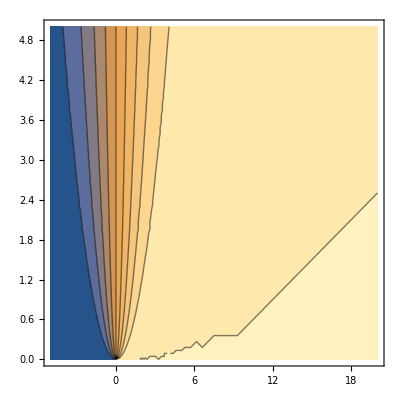

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

```mathematica
Assuming[k>0&&t>0,1/(√(4π k t))∫_(-∞)^∞ ⅇ^((-(x-y)^2)/(4k t))(-Sign[y])ⅆy//FullSimplify]
Assuming[k>0&&t>0,1/(√(4π k t))∫_(-∞)^0 ⅇ^((-(x-y)^2)/(4k t))ⅆy-1/(√(4π k t))∫_0^∞ ⅇ^((-(x-y)^2)/(4k t))ⅆy//FullSimplify]
Manipulate[Plot[Erf[x/(2 √(k t))]/.{k->1},{x,-20,20}],{t,0,5}]
ContourPlot[Erf[x/(2 √(k t))]/.{k->1},{x,-5,20},{t,0,5}]
```

### (c)

```mathematica
Assuming[k>0&&t>0&&α∈Reals,1/(√(4π k t))∫_(-∞)^∞ ⅇ^((-(x-y)^2)/(4k t))Sin[α y]ⅆy//FullSimplify]
```

ⅇ^(-k t α^2) Sin[x α]

## Problem 3

### (b)

```mathematica
D[(u[x,t]Log[u[x,t]]), t]
```

u^(0,1)[x,t]+Log[u[x,t]] u^(0,1)[x,t]

```mathematica
D[Log[1/(u[x,t]+ⅇ)], x]
```

-(u^(1,0)[x,t])/(ⅇ+u[x,t])

### (c)

```mathematica
Φ[x_,t_]=1/(√(4π k t))ⅇ^(-x^2/(4k t));
Assuming[k>0&&t>0,-∫_(-∞)^∞ Φ[x,t]Log[Φ[x,t]]ⅆx]
```

1/2 (1+Log[4 k π t])

```mathematica
Assuming[k>0&&t>0,∫_(-∞)^∞ -ⅇ^(-x^2/(4k t))x^2/(4k t)ⅆx]
```

-√π √(k t)

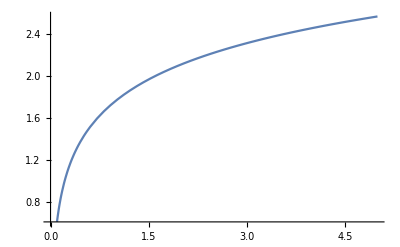

```mathematica
Plot[1/2 (1+Log[4 π t]),{t,0,5}]
```

## Problem 5

### (b)

```mathematica
u[x_,t_]=-2 D[ϕ[x,t], x]/ϕ[x,t];
D[u[x,t], t]//FullSimplify
D[u[x,t], x]//FullSimplify
D[u[x,t], x,x]//FullSimplify
```

(2 ϕ^(0,1)[x,t] ϕ^(1,0)[x,t]-2 ϕ[x,t] ϕ^(1,1)[x,t])/ϕ[x,t]^2

(2 ((ϕ^(1,0)[x,t])^2-ϕ[x,t] ϕ^(2,0)[x,t]))/ϕ[x,t]^2

-(2 (2 (ϕ^(1,0)[x,t])^3-3 ϕ[x,t] ϕ^(1,0)[x,t] ϕ^(2,0)[x,t]+ϕ[x,t]^2 ϕ^(3,0)[x,t]))/ϕ[x,t]^3

```mathematica
D[u[x,t], t]+u[x,t]D[u[x,t], x]-D[u[x,t], x,x]==0//FullSimplify
```

ϕ^(1,1)[x,t]+(ϕ^(1,0)[x,t] (-ϕ^(0,1)[x,t]+ϕ^(2,0)[x,t]))/ϕ[x,t]==ϕ^(3,0)[x,t]

### (c)

```mathematica
∫_0^x -Sign[y]ⅆy
```

ConditionalExpression[-x Sign[x], x≠0]

```mathematica
sol=Assuming[k>0&&t>0,1/(√(4π k t))∫_(-∞)^0 ⅇ^((-(x-y)^2)/(4k t))C[1] ⅇ^(-1/2 y)ⅆy+1/(√(4π k t))∫_0^∞ ⅇ^((-(x-y)^2)/(4k t))C[1] ⅇ^(1/2 y)ⅆy]
```

1/2 ⅇ^(1/4 (k t+2 x)) C[1] (1+Erf[(k t+x)/(2 √(k t))])+1/2 ⅇ^(1/4 (k t-2 x)) C[1] Erfc[(-k t+x)/(2 √(k t))]

(Erfc[(-k t+x)/(2 √(k t))]+ⅇ^x (-2+Erfc[(k t+x)/(2 √(k t))]))/(ⅇ^x (1+Erf[(k t+x)/(2 √(k t))])+Erfc[(-k t+x)/(2 √(k t))])

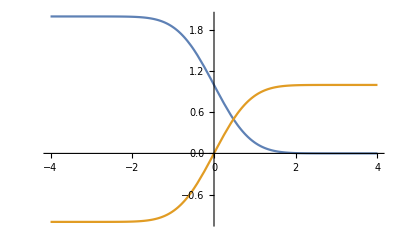

General::munfl: Exp[-799.935] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-735.964] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-799.935] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-735.964] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
ϕ[x_,t_]=sol;
u[x,t]//FullSimplify
Manipulate[Plot[{u[x,t]/.{k->0.5},(2-2 ⅇ^x)/(2+2 ⅇ^x)},{x,-4,4},PlotRange->{{-4,4},{-1,1}}],{t,0.01,5}]
Plot[{Erfc[x],Erf[x]},{x,-4,4}]
```

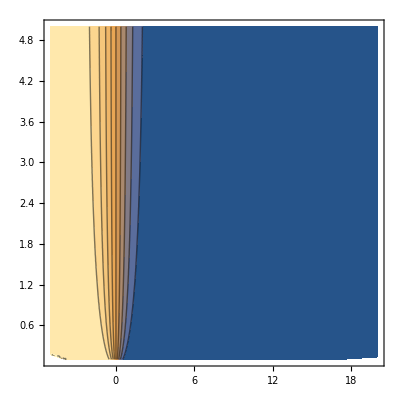

```mathematica
ContourPlot[u[x,t]/.{k->1},{x,-5,20},{t,0.1,5},PlotPoints->50]
```

```mathematica
uu[x_,t_]=FullSimplify[u[x,t]]
```

(Erfc[(-k t+x)/(2 √(k t))]+ⅇ^x (-2+Erfc[(k t+x)/(2 √(k t))]))/(ⅇ^x (1+Erf[(k t+x)/(2 √(k t))])+Erfc[(-k t+x)/(2 √(k t))])

```mathematica
D[u[x,t], t]+u[x,t]D[u[x,t], x]-D[u[x,t], x,x]/.{x->-5,t->2,k->1}//N
```

-2.97071×10^-17